```mathematica
g[f_,k_]:=Sum[Binomial[k,j]f[j],{j,0,k}]
h[f_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]g[f,j],{j,0,k}]
pl[n_]:=1/(n+1)
```

```mathematica
Table[g[pl,k],{k,0,20}]
Table[h[pl,k],{k,0,20}]
```

{1,3/2,7/3,15/4,31/5,21/2,127/7,255/8,511/9,1023/10,2047/11,1365/4,8191/13,16383/14,32767/15,65535/16,131071/17,29127/2,524287/19,209715/4,299593/3}

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D2[n_,0]:=UnitStep[n-1]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}]
Dz[n_,z_]:=Sum[(-1)^k bin[z,k]D2[n,k],{k,0,Log2@n}]
```

```mathematica
Expand@Dz[100,z]
```

1-(6088 z)/15+(148229 z^2)/360-(1873 z^3)/16+(1835 z^4)/144-(137 z^5)/240+(7 z^6)/720

```mathematica
Integrate[D[t^z,t] f[x],{t,0,x}]
```

ConditionalExpression[x^z f[x],Re[z]>0]

```mathematica
D[t^z,t]/.z->-1
```

-1/t^2

```mathematica
Integrate[t^(-1+z) z f[x],{t,0,x}]
```

ConditionalExpression[x^z f[x],Re[z]>0]

```mathematica
ff[n_]:=1
iff[n_]:=n
g[f_,x_,k_]:=Integrate[ t^(k-1)/(k-1)!f[x-t],{t,0,x}]
```

```mathematica
g[iff,n,-1/2]
```

Integrate::idiv: Integral of -n/2\ √π\ t^3/2 + 1/2\ √π\ √t does not converge on {0, n}.

∫_0^n -(n-t)/(2 √π t^(3/2))ⅆt

```mathematica
ml[n_]:=1
vs[n_]:=1;ws[n_]:=(-1)^(n+1)
vs2[n_]:=-1;ws2[n_]:=-1
vs3[n_]:=(-1)^(n+1)/n;ws3[n_]:=1/n!

Clear[F,ff,g,G,h, F2]
F[f_,n_,0]:=UnitStep[n-1]
F[f_,n_,k_]:=F[f,n,k]=Sum[f[j]F[f,Floor[n/j],k-1],{j,2,n}]
ff[f_,n_,k_]:=F[f,n,k]-F[f,n-1,k]
g[f_,v_,n_]:=g[f,v,n]=Sum[v[k]ff[f,n,k],{k,1,Log2@n}]
G[f_,v_,n_,0]:=UnitStep[n-1]
G[f_,v_,n_,k_]:=G[f,v,n,k]=Sum[g[f,v,j]G[f,v,Floor[n/j],k-1],{j,2,n}]
gg[f_,v_,n_,k_]:=G[f,v,n,k]-G[f,v,n-1,k]
h[f_,v_,w_,n_]:=h[f,v,w,n]=Sum[w[k]gg[f,v,n,k],{k,1,Log2@n}]
F2[f_,v_,w_,n_,0]:=UnitStep[n-1]
F2[f_,v_,w_,n_,k_]:=F2[f,v,w,n,k]=Sum[h[f,v,w,j]F2[f,v,w,Floor[n/j],k-1],{j,2,n}]
```

```mathematica
Table[g[ml,vs, n],{n,1,20}]
```

{1,2,3,8,5,18,7,32,18,30,11,96,13,42,45,128,17,144,19,160}

```mathematica
Table[h[ml,vs,ws, n],{n,1,20}]
```

{-1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
G[ml,vs3,100,1]
```

428/15

```mathematica
F2[ml,vs3,ws3,100,1]
```

99

```mathematica
F[ml,100,1]
```

99

```mathematica
ml[n_]:=n
vs[n_]:=1;ws[n_]:=(-1)^(n+1)
vs2[n_]:=-1;ws2[n_]:=-1
vs3[n_]:=(-1)^(n+1)/n;ws3[n_]:=1/n!

Clear[aF,aff,ag,aG,ah,aF2]
aF[f_,n_,0]:=UnitStep[n]
aF[f_,n_,k_]:=aF[f,n,k]=Sum[f[j]aF[f,n-j,k-1],{j,1,n}]
aff[f_,n_,k_]:=aF[f,n,k]-aF[f,n-1,k]
ag[f_,v_,n_]:=ag[f,v,n]=Sum[v[k]aff[f,n,k],{k,1,n}]
aG[f_,v_,n_,0]:=UnitStep[n]
aG[f_,v_,n_,k_]:=aG[f,v,n,k]=Sum[ag[f,v,j]aG[f,v,n-j,k-1],{j,1,n}]
agg[f_,v_,n_,k_]:=aG[f,v,n,k]-aG[f,v,n-1,k]
ah[f_,v_,w_,n_]:=ah[f,v,w,n]=Sum[w[k]agg[f,v,n,k],{k,1,n}]
aF2[f_,v_,w_,n_,0]:=UnitStep[n]
aF2[f_,v_,w_,n_,k_]:=aF2[f,v,w,n,k]=Sum[ah[f,v,w,j]aF2[f,v,w,n-j,k-1],{j,1,n}]
```

```mathematica
aF2[ml,vs,ws,10,1]
```

55

```mathematica
aF[ml,10,1]
```

55

```mathematica
aG[ml,vs2,10,1]
```

-10945

```mathematica
bs[n_]:=Binomial[2,n]
al[f_,1,k_]:=f[k]
al[f_,n_,k_]:=Sum[al[f,1,j]al[f,n-1,k-j+1],{j,1,k}]
b[f_,1]:=1/al[f,1,1]
b[f_,k_]:=-1/al[f,k,1]Sum[b[f,j]al[f,j,k-j+1],{j,1,k-1}]
```

```mathematica
bo2[n_]:=Binomial[2,n]
{Table[b[bo2,n],{n,1,10}],Table[D[(1+x)^(1/2),{x,k}]/k!/.x->0,{k,1,10}]}
```

{{1/2,-1/8,1/16,-5/128,7/256,-21/1024,33/2048,-429/32768,715/65536,-2431/262144},{1/2,-1/8,1/16,-5/128,7/256,-21/1024,33/2048,-429/32768,715/65536,-2431/262144}}

```mathematica
bo3[n_]:=Binomial[3,n]
{Table[b[bo3,n],{n,1,10}],Table[D[(1+x)^(1/3),{x,k}]/k!/.x->0,{k,1,10}]}
```

{{1/3,-1/9,5/81,-10/243,22/729,-154/6561,374/19683,-935/59049,21505/1594323,-55913/4782969},{1/3,-1/9,5/81,-10/243,22/729,-154/6561,374/19683,-935/59049,21505/1594323,-55913/4782969}}

```mathematica
bo32[n_]:=Binomial[3.2,n]
{Table[b[bo32,n],{n,1,10}],Table[D[(1+x)^(1/(3.2)),{x,k}]/k!/.x->0,{k,1,10}]}
```

{{0.3125,-0.107422,0.0604248,-0.0405979,0.029941,-0.0233914,0.0190055,-0.0158874,0.0135705,-0.0117894},{0.3125,-0.107422,0.0604248,-0.0405979,0.029941,-0.0233914,0.0190055,-0.0158874,0.0135705,-0.0117894}}

```mathematica
bn2[n_]:=Pochhammer[2,n]/n!
{Table[b[bn2,n],{n,1,10}],Table[D[-1/(1+x)^(1/2),{x,k}]/k!/.x->0,{k,1,10}]}
```

{{1/2,-3/8,5/16,-35/128,63/256,-231/1024,429/2048,-6435/32768,12155/65536,-46189/262144},{1/2,-3/8,5/16,-35/128,63/256,-231/1024,429/2048,-6435/32768,12155/65536,-46189/262144}}

```mathematica
bn3[n_]:=Pochhammer[3,n]/n!
{Table[b[bn3,n],{n,1,10}],Table[D[-1/(1+x)^(1/3),{x,k}]/k!/.x->0,{k,1,10}]}
```

{{1/3,-2/9,14/81,-35/243,91/729,-728/6561,1976/19683,-5434/59049,135850/1594323,-380380/4782969},{1/3,-2/9,14/81,-35/243,91/729,-728/6561,1976/19683,-5434/59049,135850/1594323,-380380/4782969}}

```mathematica
Sum[x^k,{k,0,Infinity}]
```

1/(1-x)

```mathematica
Table[(-1)^k Binomial[-1,k],{k,0,10}]
```

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Sum[ Pochhammer[z,k]/k! x^k,{k,0,Infinity}]
```

(1-x)^-z

```mathematica
Sum[ Pochhammer[z,k]/k! Binomial[x,k],{k,0,Infinity}]
```

Hypergeometric2F1[-x,z,1,-1]

```mathematica
Sum[ Pochhammer[z,k]/k! x^k/k!,{k,0,Infinity}]
```

Hypergeometric1F1[z,1,x]

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D2[n_,0]:=UnitStep[n-1]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}]
Dz[n_,z_]:=Sum[ bin[z,k]D2[n,k],{k,0,Log2@n}]
Cz[n_,z_]:=Sum[Pochhammer[z,k]/k! D2[n,k],{k,0,Log2@n}]
cz[n_,z_]:=cz[n,z]=Cz[n,z]-Cz[n-1,z]
C2z[n_,z_]:=Sum[Pochhammer[z,k]/k! D2[n,2k],{k,0,Log2@n}]
c2z[n_,z_]:=c2z[n,z]=C2z[n,z]-C2z[n-1,z]
C3z[n_,z_]:=Sum[Pochhammer[z,k]/k! D2[n,3k],{k,0,Log2@n}]
c3z[n_,z_]:=c3z[n,z]=C3z[n,z]-C3z[n-1,z]
```

```mathematica
Expand@Dz[100,z]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Expand@Cz[100,z]
```

1+(6088 z)/15+(148229 z^2)/360+(1873 z^3)/16+(1835 z^4)/144+(137 z^5)/240+(7 z^6)/720

```mathematica
Expand[C2z[100,z]]
```

1+(1132 z)/3+(191 z^2)/2+(7 z^3)/6

```mathematica
Expand@C2z[100,z]
```

1+(1132 z)/3+(191 z^2)/2+(7 z^3)/6

```mathematica
Table[FullSimplify@cz[n,z],{n,1,10}]//TableForm
```

```mathematica
Expand@Sum[cz[j,-z]c2z[k,z],{j,1,100},{k,1,100/j}]
```

1-(428 z)/15+(16289 z^2)/360-(331 z^3)/16+(611 z^4)/144-(67 z^5)/240+(7 z^6)/720

```mathematica
D[C2z[100,-z]+Cz[100,z],z]/.z->0
```

428/15

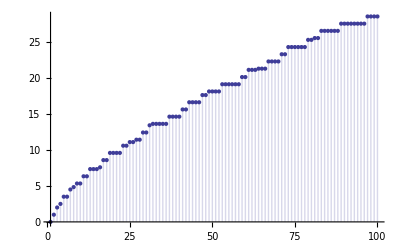

```mathematica
DiscretePlot[D[Sum[cz[j,z]c2z[k,-z],{j,1,n},{k,1,n/j}],z]/.z->0,{n,1,100}]
```

```mathematica
DiscretePlot[D[Cz[n,z]-C2z[n,z],z]/.z->0,{n,1,100}]
```

-Graphics-

```mathematica
Daz[n_,z_]:=Sum[bin[z,k] bin[n,k],{k,0,n}]
Caz[n_,z_]:=Sum[Pochhammer[z,k]/k! bin[n,k],{k,0,n}]
caz[n_,z_]:=caz[n,z]=Caz[n,z]-Caz[n-1,z]
Ca2z[n_,z_]:=Sum[Pochhammer[z,k]/k!bin[n,2k],{k,0,n}]
ca2z[n_,z_]:=ca2z[n,z]=Ca2z[n,z]-C2z[n-1,z]
```

```mathematica
Table[D[Expand@Caz[n,z],z]/.z->0,{n,1,10}]
```

{1,5/2,29/6,103/12,887/60,1517/60,18239/420,63253/840,332839/2520,118127/504}

```mathematica
FullSimplify[Sum[(2^k-1)/k,{k,1,n}]]
```

-ⅈ π-HarmonicNumber[n]-2^(1+n) LerchPhi[2,1,1+n]

```mathematica
ap[n_]:=Sum[HarmonicNumber[Floor[n/2^k]],{k,0,10}]
```

```mathematica
Table[FullSimplify[-ⅈ π-HarmonicNumber[n]-2^(1+n) LerchPhi[2,1,1+n]],{n,1,10}]
```

{1,5/2,29/6,103/12,887/60,1517/60,18239/420,63253/840,332839/2520,118127/504}

```mathematica
Table[ap[n],{n,1,10}]
```

{1,5/2,17/6,55/12,287/60,317/60,2279/420,6133/840,18679/2520,3887/504}

```mathematica
Table[D[Expand@ca2z[n,z],z]/.z->0,{n,1,10}]
```

{0,1,3,13/2,23/2,131/6,227/6,835/12,497/4,4509/20}

```mathematica
D[Cz[100,z],z]/.z->0
```

6088/15

```mathematica
Product[(1+x^(2^k)),{k,0,Infinity}]
```

1/(1-x)

```mathematica
FullSimplify@Sum[Binomial[z,k]Binomial[x,k],{k,0,Infinity}]
```

Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])

```mathematica
FullSimplify[Sum[Pochhammer[z,k]/k!Pochhammer[x,k]/k!,{k,0,Infinity}]]
```

Gamma[1-x-z]/(Gamma[1-x] Gamma[1-z])

```mathematica
Sum[Pochhammer[z,k]/k!Pochhammer[x,k]/k!,{k,0,Infinity}]/.x->3.1/.z->7.2
```

0.000230246

```mathematica
(-3.1-7.2)!/(-3.1)!/(-7.2)!
```

0.000230246

```mathematica
FullSimplify[Sum[Pochhammer[z,k]/k!Binomial[x,k],{k,0,Infinity}]]
```

Hypergeometric2F1[-x,z,1,-1]

```mathematica
FullSimplify[Hypergeometric2F1[-x,z,1,-1]-(Hypergeometric2F1[-x,z,1,-1]/.x->x-1)]
```

-Hypergeometric2F1[1-x,z,1,-1]+Hypergeometric2F1[-x,z,1,-1]

```mathematica
FullSimplify[Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])-(Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])/.x->x-1)]
```

Gamma[x+z]/(Gamma[1+x] Gamma[z])

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]]Binomial[-z,p[[2]]],{p,FI[n]}]
ap1[z_,x_]:=Gamma[x+z]/(Gamma[1+x] Gamma[z])
dza[n_,z_]:=Product[ap1[z,p[[2]]],{p,FI[n]}]
ap2[z_,x_]:=-Hypergeometric2F1[1-x,z,1,-1]+Hypergeometric2F1[-x,z,1,-1]
cza[n_,z_]:=Product[ap2[z,p[[2]]],{p,FI[n]}]
Clear[D2]
D2[n_,0]:=UnitStep[n-1]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}]
Cz[n_,z_]:=Sum[Pochhammer[z,k]/k! D2[n,k],{k,0,Log2@n}]
cz[n_,z_]:=cz[n,z]=Cz[n,z]-Cz[n-1,z]
Clear[Dza,dza]
Dza[n_,z_,a_]:=Dza[n,z,a]=Sum[bin[z,k]D2[n,2^a k],{k,0,Log2@n}]
dza[n_,z_,a_]:=dza[n,z,a]=Dza[n,z,a]-Dza[n-1,z,a]
```

```mathematica
rr[n_,z_]:=Sum[dza[a,z,0]dza[b,z,1]dza[c,z,2]dza[d,z,3]dza[e,z,4]dza[f,z,5],{a,1,n},{b,1,n/a},{c,1,n/a/b},{d,1,n/a/b/c},{e,1,n/a/b/c/d},{f,1,n/a/b/c/d/e}]
```

```mathematica
Expand@rr[10,z]
```

1+(40 z)/3+(9 z^2)/2+z^3/6

```mathematica
Expand@Cz[10,z]
```

1+(40 z)/3+(9 z^2)/2+z^3/6

```mathematica
Table[Expand@Dza[4100,z,k],{k,0,4}]//TableForm
```

1+(16042379 z)/27720+(144719059 z^2)/103950+(474203123 z^3)/362880+(962678897 z^4)/1555200+(35600083 z^5)/207360+(1203158941 z^6)/43545600+(1357597 z^7)/483840+(2392231 z^8)/14515200+(1607 z^9)/290304+(601 z^10)/6220800+z^11/2280960+z^12/479001600
1-(464483 z)/60+(1820813 z^2)/90+(640999 z^3)/48+(101555 z^4)/144+(299 z^5)/80+z^6/720
1+(729965 z)/6+8912 z^2+z^3/6
1+17825 z
1

```mathematica
D[Cz[100,z]-C2z[100,z],z]/.z->0
```

428/15

```mathematica
D[Sum[Dza[100,z,k],{k,0,5}],z]/.z->0
```

6088/15

```mathematica
D[Cz[100,z],z]/.z->0
```

6088/15

```mathematica
FullSimplify[Pochhammer[z+1,x]/x!]
```

Pochhammer[1+z,x]/(x!)

```mathematica
(z+x)!/z!/x! = Multiset[z+1,x] = Multiset[x+1,z]
```

```mathematica
mset[z_,x_]:=Pochhammer[z,x]/x!
mset2[z_,x_]:=(z+x)!/z!/x!
```

```mathematica
mset[13+1,5]
```

8568

```mathematica
mset[5+1,13]
```

8568

```mathematica
mset2[5,13]
```

8568

```mathematica
Table[Cz[100,z],{z,0,12}]
```

{1,949,3619,9263,19591,36857,63952,104504,162985,244825,356533,505825,701759}